```mathematica
NotebookEvaluate[NotebookDirectory[]<>"FEM_tools_coh.nb"];
```

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"MeshRefinement_tools.nb"];
```

```mathematica
AbortOnMessage[]
```

```mathematica
L=1.;dx=L/20;udim=3;ndim=3;
(*rg=MyRegionDifference[Rectangle[{0,0},{L,L}],ImplicitRegion[(x-L/2)^2+(y-L/2)^2< L^2/64,{x,y}]];
rg=ImplicitRegion[0≤x≤L&& 0≤y≤L,{x,y}];*)
(*rg=Cuboid[{0,0,0},{L,L,0.05 L}];
{m1,coord,ele,eleB,eleP}=Region2Mesh[rg,dx^3,1,0];*)


coord=N[Region2Points[{0,0,0},{L,L,0.1 L},dx]];Clear[funR];
funR[x_,y_,z_]:=(y+x<L+4dx  && y-(x-L)^2>-8dx && x>0.4L);
{coord,ele}=DelaunayMeshWithRefinement[coord,funR];
funR[x_,y_,z_]:=(x+y<L+2dx && y-(x-L)^2>-4dx && x>0.44L);
{coord,ele}=DelaunayMeshWithRefinement[coord,funR];
funR[x_,y_,z_]:=(x+y<L+0.5dx && y-(x-L)^2>-2dx && x>0.48L);
{coord,ele}=DelaunayMeshWithRefinement[coord,funR];
hole3fun[x_,y_,z_]:=y>=0.5 L-1dx && y<=0.5 L-0.01dx && x<=0.5 L
{ele,coord}=RemoveElementByFunctions[ele,coord,hole3fun];
(*goodEle=SimplexMeshCheckRegularQuality[coord,ele];*)
```

```mathematica
(*ele=ele[[goodEle]];*)
m1=Abaqus2Mesh[coord,ele];
ShowMesh[m1]
```

-Graphics3D-

```mathematica
0.1/dx^3
```

1.9683×10^6

```mathematica
ele//Dimensions
```

{376920,4}

```mathematica
faceLeft={{0,0,0}-0.05 dx,{L,0,0.1L}+0.01 dx};
fixList=FindPoints[coord,faceLeft[[1]],faceLeft[[2]]];
pDirichlet=10.^8;
fixFun[xyz_List]:=ConstantArray[0,ndim];
fixValues=BCValuesFunc[fixList,coord,fixFun,ndim];
dofFix=DofIndexValue[fixList,fixValues];

faceList=FindPoints[coord,{0,L,0}-0.01dx,{L,L,0.1 L}+0.001dx];
fixU=faceList;
fixFun2[xyz_List]:={0.,-10.^-3};
fixFun2[xyz_List]:=10.^-3{1,0,0};
fixValues2=BCValuesFunc[faceList,coord,fixFun2,ndim];
dofFix2=DofIndexValue[faceList,fixValues2];
dofFix=Join[dofFix,dofFix2,2];
```

```mathematica
(*eleNoDamage={};FindElement[coord,ele,{0.4,0.25},{0.5,0.5}];eleNoDamage={};*)
```

```mathematica
gpr=(*Q9ic3m;*)(*Q4ic2m*)O1ic15m;endn=ElementShapeNdN["O1"(*"Q2S"*),gpr];endnN=endn[[All,1]];endndN=endn[[All,2;;]];
weighL=gpr[[All,-1]];

gprB=T1ic12m;(*L2ic21m;*)
endnB=ElementShapeNdN["S1",gprB];endnNB=endnB[[All,1]];endndNB=endnB[[All,2;;]];
weighLB=gprB[[All,-1]];
```

```mathematica
Funϕ0ϕc[s0_,Gc_,ls_]:=Gc/ls*s0/(1-s0);
```

```mathematica
ndim
```

3

```mathematica
{Rindex,Kindex}=RKindexFEM[ele,ndim];
```

```mathematica
dx/8
```

0.00625

```mathematica
lc0= 0.9dx/2(*/2/2*);morder0=1;mat0={(*25.85 10^9, 0.18,*)210,0.3,2,2.7 10^-3 (*1000000*),lc0,0,morder0};
energyE0=Funϕ0ϕc[0.2,mat0[[4]],mat0[[5]]];AppendTo[mat0,energyE0];
islinear=True;dt=2;dt0=0.05;dtMin= 10^-4;nnode=Length[coord];ndof=nnode ndim;
uvw=ConstantArray[0.,{nnode,ndim}];pMid={1};fPMid={};ctime=0.;eH={};
(*ResiBC=ResidualOfElementSet[weighLB,endnNB,endndNB,coord,forceEle,{10.^4,0}];*)
printInterval=20;freeInterval=60000;nonlinearStep=If[islinear,1,10];incHistory={};
Hdirect=Table[0.,{Length[ele]},{Length[weighL]}];
HdirectN1=Hdirect;
HdirectN2=Hdirect;
nGP=Length[weighL];
tTotle=100;
forceList={};
tforceList=0.;
normIncL={};
```

```mathematica
mat0
```

{210,0.3,0,0.0027,0.015,0,1,0.045}

$Aborted

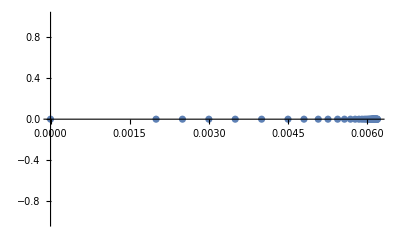
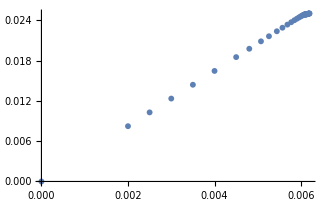
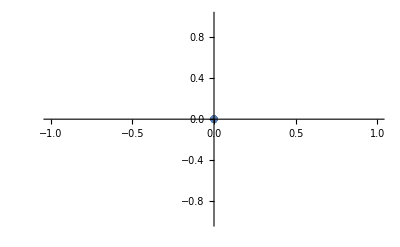
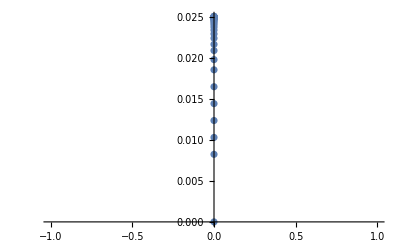

```mathematica
AbortReady[];
Do[
Label[dtHalf];
(*If[uvw[[faceList[[1]]]][[1]]>0.0005,dt=0.2 10^-3];*)
(*{clist,vlist}=AlphaMethod[duvw,uvw,dt];*)
(*nonvarList=NOMCombineVarsToArray[N[gm0],N[Df0],N[clist],N[vlist]];*)
(*HdirectMax=TwoTableMaxEach[HdirectMax,Hdirect[[All,All,1]]];
(*{Rp,Kp}=FemAllMatrixPFs[ls,weighL,endnN,endndN,coord,ele,HdirectMax];*)
{Rp,Kp}=FemAllMatrixPFsPara[ls,weighL,endnN,endndN,coord,ele,HdirectMax,RindexPf,KindexPf];
DirichletApply[Kp,Rp,pfdofFix,pDirichlet];
pfList=LinearSolve[Kp,Rp];*)
ctime+=dt;
uvwN=uvw;incT=ConstantArray[0.,ndof];
AppendTo[eH,{uvwN[[fixU[[1]]]][[2]],Max[Hdirect]/( mat0[[4]]/mat0[[5]])}];
normIncL={};
Do[
(*{Rsp,Ksp,Hdirect}=FemAllMatrixPFuvwPara[weighL,endnN,endndN,coord,uvwN,pfList,ele,Di,GcL,MohrCoumbC,Rindex,Kindex,OneElementMatrixPFuvwPara2D];*)
(*{Rsp,Ksp,Hdirect,fixElementList0,fixDirectionList0}=FemAllMatrixVD2d[weighL,endnN,endndN,coord,uvwN,Hdirect,ele,mat0,Rindex,Kindex,OneElementMatrixVD2d];*)
(*{Rsp,Ksp,Hdirect,fixElementList0,fixDirectionList0}=FemAllMatrixVD2dMix[weighL,endnN,endndN,coord,uvwN,Hdirect,ele,mat0,Rindex,Kindex,OneElementMatrix2Delastic,OneElementMatrixVD2d,OneElementMatrixFix2d,fixElementList0,fixDirectionList0,damagePara0];(*worked*)
*)
Print[AbsoluteTiming[{Rsp,Ksp,Hdirect}=FemAllMatrixVD2d[weighL,endnN,endndN,coord,uvwN,Hdirect,ele,mat0,Rindex,Kindex,OneElementMatrixVD3d];]];
(*AppendTo[KList,Rsp];*)
(*FemAllMatrixPFuvw[weighL,endnN,endndN,coord,uvwN,pfList,ele,Di,GcL,MohrCoumbC,MaximalEnergyDirection2D,WeakPlane2D];*)
(*Hdirect[[All,All,1]]*=ls;*)
Rsp*=-1.;
tforceList=Join[uvwN[[fixU[[1]]]],-{Total[ExtractNodeForce[Rsp,fixU,ndim,1]],Total[ExtractNodeForce[Rsp,fixU,ndim,2]]}];
(*Rsp+=ctime ResiBC;*)
NLDirichletApplySymF[ndim,uvwN,Ksp,Rsp,dofFix,ctime];
Print[AbsoluteTiming[uv=LinearSolve[Ksp,Rsp,Method->"Pardiso"];]];
incT+=uv;
uvwN+=Vector2Matrix[uv,udim];
normInc=Norm[uv]/(Norm[incT]+10.^-20);
If[!NumericQ[normInc],Print["Error, symbol in nomrInc;"];Abort[]];
AppendTo[normIncL,normInc];
(*Print[normInc,"it",j];*)If[Norm[uv]/(Norm[incT]+10.^-20)≤1. 10^-6,Break[]];kIti=j;If[(j==nonlinearStep || Total[normIncL]>5)&& (!islinear),Print["Warning, divergent at ctime=",ctime, " with dt=",dt];incHistory[[-1]]=100;
ctime-=dt;
dt=dt/2;
If[dt<dtMin,Print["Error, minimal time increment reached!"];Abort[]];
Goto[dtHalf]];,{j,nonlinearStep}];
If[ctime≥tTotle,Break[]];
Print["step:",i," time:",ctime];
uvw=uvwN;
dt=dt0 Max[ 10/(1+Max[Hdirect]/( mat0[[4]]/mat0[[5]]))^2, 100 10^-3];
AppendTo[forceList,tforceList];
AppendTo[incHistory,kIti];
If[kIti>15,dt=dt/2.];
If[Length[incHistory]>3 && Total[incHistory[[-3;;-1]]]<22 && !islinear,dt*=2.];
If[Mod[i-1,printInterval]==0,(*SaveToCell[uvw,"uvw"<>ToString[ctime]];*)Print[Plot3DField[uvwN[[All,1]],m1]];Print[Plot3DField[uvwN[[All,2]],m1]];(*Print[Plot2DField0[#/(#+mat0[[4]]/mat0[[5]]),m1]&[MeanGaussPointToNode[Hdirect,ele,coord]]];*)(*Print[Plot2DField[pfList,m1]]*)];
AppendTo[fPMid,uvw[[pMid]]];
(*AppendTo[resP1,Flatten[uvw[[p1]]]];*)
(*Print[Plot2DField[ acc[[All,2]],m1]];*)
(*Print[Contour2DField[ uvw[[All,1]],m1],Contour2DField[ vel[[All,1]],m1],Contour2DField[ acc[[All,1]],m1]];*)
(*Print[Contour2DField[NormList[ uvw],m1],Contour2DField[ NormList[acc],m1],Contour2DField[ NormList[vel],m1]];*)
(*Print[Contour2DField[ uvw[[All,1]],m1],Contour2DField[ uvw[[All,2]],m1],Contour2DField[ acc[[All,1]],m1]];
Print[Contour2DField[ acc[[All,2]],m1],Contour2DField[ vel[[All,1]],m1],Contour2DField[ vel[[All,2]],m1]]*)
AbortCheck[],{i,2000}];
Print["Finish all step"];
(*HnodeValue=GaussPointToNode[Hdirect,ele,coord,endnN];*)
HnodeValue=MeanGaussPointToNode[Hdirect,ele,coord];
Plot3DField[HnodeValue,m1]
Plot3DField[HnodeValue/(HnodeValue+mat0[[4]]/mat0[[5]]),m1]
SaveToCell[forceList,"Node lc:"<>ToString[Length[coord]]<>" and "<>ToString[N[lc0]]<>"fmax:"<>ToString[InputForm[Round1[forceList[[Ordering[forceList[[All,2]],-1]]],5]]]]
{ListPlot[forceList[[All,{1,3}]]],ListPlot[forceList[[All,{1,4}]]],ListPlot[forceList[[All,{2,3}]]],ListPlot[forceList[[All,{2,4}]]]}
```

{65387,3}

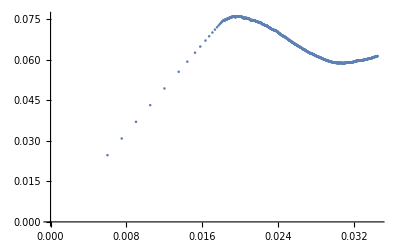

```mathematica
coord//Dimensions
```

```mathematica
Plot3DField[HnodeValue/(HnodeValue+mat0[[4]]/mat0[[5]]),m1]
```

-Graphics3D-

```mathematica
uvw
```

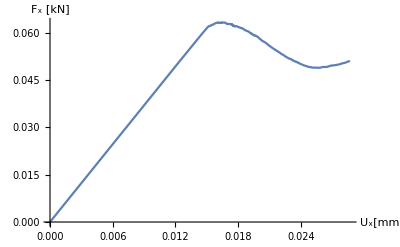

-Graphics3D-

-Graphics3D-

```mathematica
s10=2.5;
ListPlot[s10 forceList[[All,{1,4}]],Joined->True,AxesLabel->{"U_x[mm]","F_x [kN]"}]
Plot3DField[s10 uvwN[[All,1]],m1]
Plot3DField[s10 uvwN[[All,2]],m1]
```